# Math 385 HW # 3

## Mario L. Gutierrez Abed

(1) Define f(x)=sin(x)ⅇ^-x.  
(2) Plot f(x) on [2 ,4].  
(3) Write a program using the secant method to find a root near π . Make sure that the loop is conditioned on nearness exit (tolerance) and iteration limit (1000) . 
(4) Compare with FindRoot (for a secant method using the two seeds) using absolute error. 
(5) Compare with final answer from Newton’s method using absolute error.

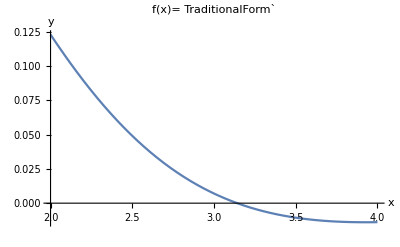

```mathematica
f[x_]=ⅇ^-x Sin[x];
Plot[f[x],{x,2,4},PlotLabel->Style["f(x)= TraditionalForm`",FontSize->15,FontColor->Purple],AxesLabel->{x,y}]
```

Now we find the root of our function between x=2 and  x=4  by programming the secant method:

```mathematica
f[x_]=ⅇ^-x Sin[x];
Subscript[x, 1]=2.0;
Subscript[x, 2] =4.0;
Subscript[x, new] = Subscript[x, 1] - f[Subscript[x, 1]]*(Subscript[x, 2]-Subscript[x, 1])/(f[Subscript[x, 2]]- f[Subscript[x, 1]]);
iterationcount = 0;
While[Abs[f[Subscript[x, new]]]> 10^-5 && iterationcount < 1000,
Subscript[x, new]= Subscript[x, 1] - f[Subscript[x, 1]]*(Subscript[x, 2]-Subscript[x, 1])/(f[Subscript[x, 2]]- f[Subscript[x, 1]]);
If[f[Subscript[x, 1]]*f[Subscript[x, new]]>0,
Subscript[x, 1]= Subscript[x, new],
Subscript[x, 2] = Subscript[x, new]
];
iterationcount++;
];
Subscript[x, new]
iterationcount
```

3.14179

18

Now we find our root using the built-in function FindRoot (for the secant method):

```mathematica
secroot = FindRoot[f[x],{x,2.0,4.0}];
secroot = secroot⟦1⟧⟦2⟧
```

3.14159

Now we compare the value of our root obtained by programming the secant method with the value given by the built-in function FindRoot (for the secant method):

```mathematica
Abs[Subscript[x, new]-secroot]//ScientificForm
```

2.0082×10^-4

Lastly we compare the value of our root obtained by programming the secant method with the value obtained by programming Newton’s method (from the previous homework). First we run Newton’s method to obtain the root x_0 and then we look at the absolute-value error associated between this value and x_new:

```mathematica
newt[x_]=ⅇ^-x Sin[x];
g[x_]= D[newt[x],x];
Subscript[x, 0]=2.0;
count = 0;
While[Abs[newt[Subscript[x, 0]]]> 10^-5,
Subscript[x, 0] = (g[Subscript[x, 0]]*Subscript[x, 0] - newt[Subscript[x, 0]])/g[Subscript[x, 0]];
count++
];
Subscript[x, 0]
count
```

3.14141

4

```mathematica
Abs[Subscript[x, new]- Subscript[x, 0]]//ScientificForm
```

3.85593×10^-4

This value is the upper bound for errors. In other words, even when the value of the actual root that we’re looking for is still unknown, we know that the absolute value of the difference between the Newton’s method approximation and the secant method approximation is the largest error we can possibly have (i.e. the actual root MUST lie between the root values given by the secant method and Newton’s method. )